# Knockout (Normal Kinematics)

```mathematica
c=299.792458;(* mm/ns *)
u = 931.494;
mp=938.27203;
mn=939.56536;
md=1875.612793;
mHe4=3728.401;
mB11=10255.1;
mC12=11178;
mN13=12114.77;
mN21=19586.63;
mO13=12132.54;
mO14=13048.92;
mO21=19569.44;
mO22=20502.15;
mO23=21438.98;
mO24=22374.93;
mF19=17696.9;
mF23=21427.69;
mF24=22363.42;
mCl35=32573.28; (* 75% *)
mCl37=34433.52; (* 25% *)
massList={mp->"π",mn->"μ",mHe4->"α",mB11->"B11",mC12->"C12",mN13->"N13",mN21->"N21",mO13->"O13",mO14->"O14",mO21->"O21",mO22->"O22",mF19->"F19",mF23-> "F23", mCl35->"C135",mCl37->"Cl37"};
```

## Functions

```mathematica
(* all angel in radian, except for display *)
```

### Titled Lorentz Transfrom

The Lorentz Tranform on aribtary direction is well discrpted in Goldstien P .281

```mathematica
(* basis right-hand rotation operator *)
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}};
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}};
(* coordinate transform *)
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[-ϕ].Ry[-θ].Lz[β].Ry[θ].Rz[ϕ]
```

### Rotation on (θ, ϕ) from Left Side

```mathematica
R[ϕNN_,θ_,ϕ_]:=Rz[-ϕ].Ry[-θ].Rz[ϕNN].Ry[θ].Rz[ϕ];
```

```mathematica
Manipulate[Graphics3D[{
{Gray,Line[{{0,0,0},{1,0,0}}]},
Text["x",{1,0,0}],
{Gray,Line[{{0,0,0},{0,1,0}}]},
Text["y",{0,1,0}],
{Gray,Line[{{0,0,0},{0,0,1}}]},
Text["z",{0,0,1}],
{Red,Arrow[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]},
{Blue,Arrow[{{0,0,0},{Cos[θNN] Cos[ϕ] Sin[θ]+Sin[θNN] (Cos[θ] Cos[ϕ] Cos[ϕNN]-Sin[ϕ] Sin[ϕNN]),Cos[θNN] Sin[θ] Sin[ϕ]+Sin[θNN] (Cos[θ] Cos[ϕNN] Sin[ϕ]+Cos[ϕ] Sin[ϕNN]),Cos[θ] Cos[θNN]-Cos[ϕNN] Sin[θ] Sin[θNN]}}]}
},PlotRange->1,ViewPoint->{15,10,7}],{θ,0,π},{ϕ,0,2π},{θNN,0,π},{ϕNN,0,2π}]
```

### basic convertors

```mathematica
Mass[E_,k_]:=√(E^2-k^2);
Momentum[A_]:=Norm[A[[2;;4]]];
k2T[k_,m_]:=√(m^2+k^2)-m;
KE[A_,m_]:=A[[1]]-m
T2k[T_,m_]:=√(2m T+T^2);
(* θ(0,π), ϕ(-π,π) *)
Angle[A_]:=If[A[[2]]==0 && A[[3]]==0,{If[A[[4]]>0,0,π],0},{ArcTan[A[[4]],√(A[[2]]^2+A[[3]]^2)],ArcTan[A[[2]],A[[3]]]}];
ϕCorr[ϕ_]:=If[ϕ>0,π-ϕ,-ϕ-π]
(* angle between 2 vector*)
ΔAngle[A_,B_]:=ArcCos[(A[[2]]B[[2]]+A[[3]]B[[3]]+A[[4]]B[[4]])/(Momentum[A]Momentum[B])];
(* Display DisVector *)
DisVector[A_,name_]:={name,A[[1]],A[[2]],A[[3]],A[[4]]}
(* display (K.E. , momentum, angle 0 *)
β[A_]:=Momentum[A]/A[[1]]
DisEnergy[A_,m_,name_]:={name,A[[1]]-m,Momentum[A],Angle[A][[1]] ,Angle[A][[2]]}
```

```mathematica
(* 2 way to declare momentum 4-vector *)
PX[EX_,kX_,θX_,ϕX_]:={EX,kX Sin[θX]Cos[ϕX],kX Sin[θX]Sin[ϕX],kX Cos[θX]};
P[T_,m_,θ_,ϕ_]:={m+T,T2k[T,m]Sin[θ] Cos[ϕ],T2k[T,m] Sin[θ]Sin[ϕ],T2k[T,m] Cos[θ]};
```

### Detectors Geometry

```mathematica
FL[V_]:=(2 1400)/(√3 Abs[Cos[Angle[V][[2]]]]Sin[Angle[V][[1]]]+Cos[Angle[V][[1]]])
ToF[V_]:=FL[V]/(β[V]c)
Sp[V1_,V2_,T_]:=Module[{β,γ},
γ=(mp+T)/mp;
β=√(1-1/γ^2);
(1+γ)mp-γ(V1[[1]]+V2[[1]])+γ β(V1[[4]]+V2[[4]])]
SpFullNK[P1_,P2_,mInc_,mTar_,T_]:=√((mInc+T+mTar-P1[[1]]-P2[[1]])^2-Momentum[PX[mInc+T,√(2mInc T+T^2),0,0]-P1-P2]^2)-(mTar-mInc);
SpNK[P1_,P2_,T_]:=T+mp+mp-P1[[1]]-P2[[1]]
f[x_]:=Piecewise[{{3/2(x+170),200 2/3-170>x>-170},{200,200 (-2/3)+950>x>200 2/3-170},{-3/2(x-950),950>x>200 (-2/3)+950}},-1]
```

```mathematica
Observable[list_]:=Monitor[Table[{
(*1 *) FL[list[[i,1]]],
(*2 *) FL[list[[i,2]]],
(*3 *) ToF[list[[i,1]]],
(*4 *) ToF[list[[i,2]]],
(*5 *) Angle[list[[i,1]]],
(*6 *) Angle[list[[i,2]]],
(*7 *) KE[list[[i,1]],mp],
(*8 *) KE[list[[i,2]],mp],
(*9 *) β[list[[i,1]]],
(*10 *) β[list[[i,2]]],
(* 11 *) Sp[list[[i,1]],list[[i,2]],260],
(* 12 *) KE[list[[i,1]],mp]+KE[list[[i,2]],mp],
(*13 *)SpFullNK[list[[i,1]],list[[i,2]],mp,mp,260],
(*14 *)SpNK[list[[i,1]],list[[i,2]],260]
},{i,1,Length[list]}],i]
```

### Simulation

```mathematica
knockout[k_,θk_,ϕk_,θNN_,ϕNN_,S_,mTar_,mInc_,m_,TInc_]:={
PI=PX[mInc+TInc,√(2mInc TInc+TInc^2),0,0];
Pn=PX[mTar-√((mTar-m+S)^2+k^2),k,θk,ϕk]; (* fake 4 vector, for construct the CM frame of a-X*)
Pc=(PI+Pn)/2;
βPc=β[Pc];
{θPc,ϕPc}=Angle[Pc];
(* in CM frame of a X *)
Pcc=Pc.L[-βPc,θPc,ϕPc];
PIc=PI.L[-βPc,θPc,ϕPc];
Pnc=Pn.L[-βPc,θPc,ϕPc];
{θIc,ϕIc}=Angle[PIc];
Etotal=√(1-βPc^2)(PI[[1]]+Pn[[1]]); (* total energy of E1c and E2c *)
k1c=1/(2 Etotal)(√((Etotal-mInc-m)(Etotal+mInc-m) (Etotal-mInc+m) (Etotal+mInc+m)));
P1c={√(mInc^2+k1c^2),k1c Sin[θIc+θNN]Cos[ϕIc],k1c Sin[θIc+θNN]Sin[ϕIc], k1c Cos[θIc+θNN]}.R[ϕNN,θIc,ϕIc];
P2c={√(m^2+k1c^2) ,k1c Sin[θIc+θNN+π]Cos[ϕIc],k1c Sin[θIc+θNN+π]Sin[ϕIc], k1c Cos[θIc+θNN+π]}.R[ϕNN,θIc,ϕIc];
P1=P1c.L[βPc,θPc,ϕPc];
P2=P2c.L[βPc,θPc,ϕPc];
Sn=√((PI[[1]]+mTar-P1[[1]]-P2[[1]])^2-Momentum[PI-P1-P2]^2)-(mTar-m);
(* output *)
P1,P2
}
```

## Simulation

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mTar,mInc,m2,TiL];
TableForm[
{{NumberForm[TableForm[Chop[{
"Setting",{"k",k,"θk, ϕk",θk  ,ϕk  },{"S",S,"θNN, ϕNN",θNN  ,ϕNN  },
{"βPI",βPI},
{"Sn", Sn, "SpFullNK",SpFullNK[P1,P2,mInc,mTar,TiL]},
{"SpOnline",Sp[P1,P2,TiL]},
{"Nucleus frame ", "----", "----", "----"},DisVector[PI,"PI"],DisVector[Pn,"Pn"],DisEnergy[Pn,m2,""],DisVector[P1,"P1"],DisVector[P2,"P2"],DisVector[P1+P2-PI-Pn,"Diff"],
{"Lorentz", "----", "----", "----"},DisVector[Pc,"Pc"],DisEnergy[Pc,0,""],{"β" , βPc,"γ", 1/(√(1-βPc^2))},DisVector[Pcc,"pcc"],
{"CM frame", "----", "----", "----"},DisVector[PIc,"PIc"],DisVector[Pnc,"Pnc"],DisVector[P1c,"k1c"],DisVector[P2c,"P2c"]
}],TableAlignments->{Right}],6],
Graphics[{
{Purple,Arrow[{-{PI[[2]],PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1[[2]],P1[[4]]}}]},
{Red,Arrow[{{0,0},{P2[[2]],P2[[4]]}}]},
{Green,Arrow[{{0,0},{Pc[[2]],Pc[[4]]}}]},
{Orange,Arrow[{-{Pn[[2]],Pn[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],
PlotLabel-> "Nucleus, ΣT="<>ToString[KE[P1,mInc]+KE[P2,m2]]<>", Δθ="<>ToString[(Angle[P1][[1]]+Angle[P2][[1]])180/π],ImageSize->400,
Epilog->{
Text["θ1="<>ToString[Angle[P1][[1]] 180/π]<>"\n T1="<>ToString[KE[P1,mInc]],1.2{P1[[2]],P1[[4]]}],
Text["θ2="<>ToString[Angle[P2][[1]] 180/π]<>"\n T2="<>ToString[KE[P2,m2]],1.2{P2[[2]],P2[[4]]}]
}]
,
Graphics[{
{Purple,Arrow[{-{PIc[[2]],PIc[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1c[[2]],P1c[[4]]}}]},
{Red,Arrow[{{0,0},{P2c[[2]],P2c[[4]]}}]},
{Orange,Arrow[{-{Pnc[[2]],Pnc[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "C.Momemtum",
Epilog->{Text["T_tot="<>ToString[DisEnergy[PIc,mp,""][[2]]+DisEnergy[Pnc,mn,""][[2]]],{0,500}]},ImageSize->250]

}
}]
,{{mInc,mp},{mp->"Proton",mn->"Neutron"}},{{m2,mp},{mp->"Proton",mn->"Neutron",mHe4->"alpha"}},{{mTar,mC12},massList},{{TiL,250},0,280},{{k,100},0,100},{{θk,90},-180,180},{{ϕk,0},-180,180},{{S,30},0,30},{{θNN,90},-180,180},{{ϕNN,0},-180,360},ControlPlacement->Top]
```

## Monte Carlo

```mathematica
n=50000;
TInc=260;
minc=mp;
mtar=Table[
(*RandomChoice[{mp,mp,mp,mp,mp,mp,mp,mp,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12}]*)
(*RandomChoice[{mC12,mC12,mF19,mF19,mF19,mC12,mC12,mF19,mF19,mF19,mC12,mC12,mF19,mF19,mF19,mC12,mC12,mF19,mF19,mF19,mCl35,mCl35,mCl35,mCl37}]*)
mp
(*RandomChoice[{mp,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12,mC12}]*)
,{i,1,n}];
kM=Table[
If[mtar[[i]]== mp,0,RandomReal[{0,100}]]
,{i,1,n}];
SpM=Table[
Switch[mtar[[i]],
mp,0,
mC12,RandomChoice[{4.247,11.345,24.674}],
mF19,RandomChoice[{2.041,5.537,11.768,17.644,29.742}],
mCl35,RandomChoice[{1.7,4.74,7.4,12.1,18.5,22.25,31.81}],
mCl37,RandomChoice[{3.69,7.07,9.38,14.18,20.75,24.3,33.82}]
],{i,1,n}];
θkList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕkList=Table[ π RandomReal[{-1,1}],{i,1,n}];
θNNList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕNNList=Table[π RandomReal[{-1,1}],{i,1,n}];
(*DensityHistogram[
Table[{θkList[[i]],ϕkList[[i]]},{i,1,n}]
,{0.1}]*)
(* outputList = {P1L, P2L} *)
DataList=Monitor[Table[knockout[kM[[i]],θkList[[i]] ,ϕkList[[i]] ,θNNList[[i]] ,ϕNNList[[i]],SpM[[i]],mtar[[i]],minc,mp,TInc],{i,1,n}],i];
(* Rearrange Data, π/2>Angle[V][[2]]>-π/2 should be the frist*)
ArrgDataList=Monitor[Table[
If[ π/2≥ Angle[DataList[[i,1]]][[2]]≥ -π/2 ,DataList[[i]],{DataList[[i,2]],DataList[[i,1]]}]
,{i,1,n}],i];
```

```mathematica
DataObser=Observable[ArrgDataList];
```

```mathematica
Select[DataList,Im[Angle[#[[1]]][[2]]]≠ 0&][[1,1]]
```

{616.673+203.067 ⅈ,-19.0873-749.244 ⅈ,-24.025+174.197 ⅈ,377.451+304.966 ⅈ}

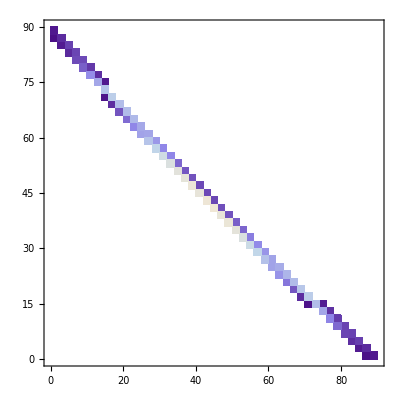

```mathematica
DensityHistogram[
Table[{DataObser[[i,5,1]],DataObser[[i,6,1]]}180/π,{i,1,n}],{{0, 100,2},{0,100,2}}
]
```

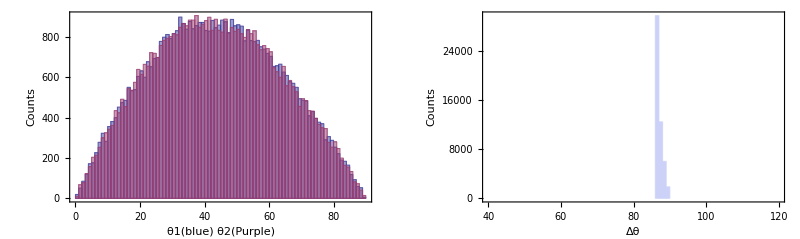

```mathematica
GraphicsGrid[{{
Histogram[{Table[DataObser[[i,5,1]] 180/π,{i,1,n}],Table[DataObser[[i,6,1]] 180/π,{i,1,n}]},Frame->True,FrameLabel-> {"θ1(blue) θ2(Purple)","Counts"}],
Histogram[Table[(DataObser[[i,5,1]]+DataObser[[i,6,1]])180/π,{i,1,n}],{40,120,1},Frame->True,FrameLabel-> {"Δθ","Counts"}]
}},ImageSize->800]
```

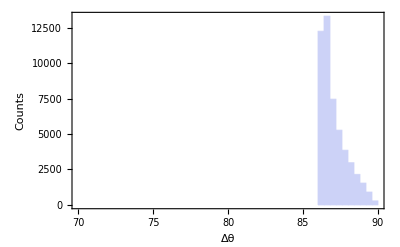

```mathematica
Histogram[Table[(DataObser[[i,5,1]]+DataObser[[i,6,1]])180/π,{i,1,n}],{70,90,0.4},Frame->True,FrameLabel-> {"Δθ","Counts"}]
```

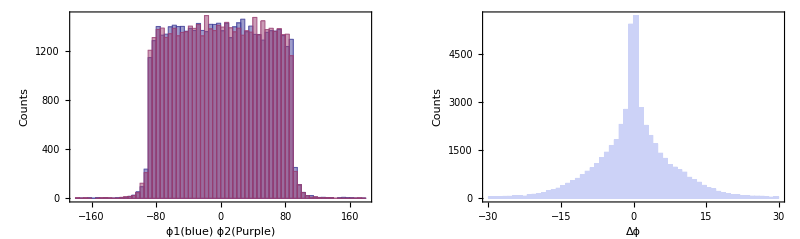

```mathematica
GraphicsGrid[{{
Histogram[{Table[DataObser[[i,5,2]] 180/π,{i,1,n}],Table[ϕCorr[DataObser[[i,6,2]]] 180/π,{i,1,n}]},Frame->True,FrameLabel-> {"ϕ1(blue) ϕ2(Purple)","Counts"}],
Histogram[Table[(DataObser[[i,5,2]]+ϕCorr[DataObser[[i,6,2]]])180/π,{i,1,n}],{-30,30,1},Frame->True,FrameLabel-> {"Δϕ","Counts"}]
}},ImageSize->800]
```

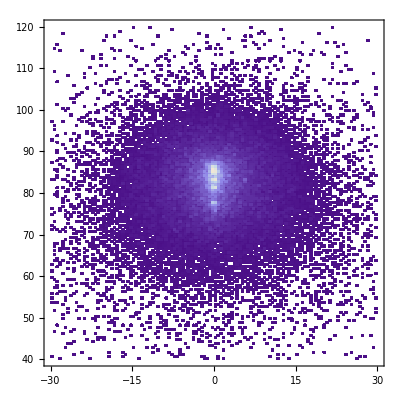

```mathematica
DensityHistogram[
Table[{(DataObser[[i,5,2]]+ϕCorr[DataObser[[i,6,2]]])180/π,(DataObser[[i,5,1]]+DataObser[[i,6,1]])180/π},{i,1,n}],{{-30,30,0.5},{40,120,0.5}}
]
```

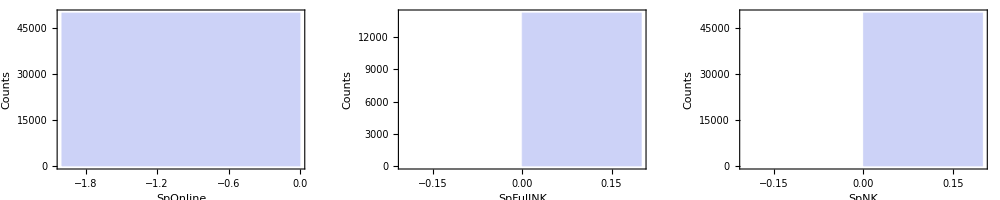

```mathematica
GraphicsGrid[{{
Histogram[Table[DataObser[[i,11]],{i,1,n}],{2},Frame->True,FrameLabel-> {"SpOnline","Counts"}],
Histogram[Table[DataObser[[i,13]],{i,1,n}],{0.2},Frame->True,FrameLabel-> {"SpFullNK","Counts"}],
Histogram[Table[DataObser[[i,14]],{i,1,n}],{0.2},Frame->True,FrameLabel-> {"SpNK","Counts"}]
}},ImageSize->1000]
```

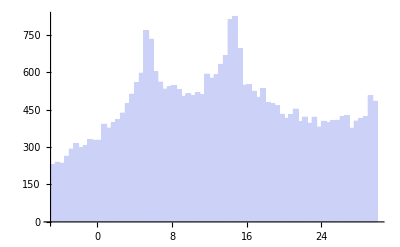

```mathematica
Histogram[Table[DataObser[[i,11]],{i,1,n}],{-5,30,0.5}]
```

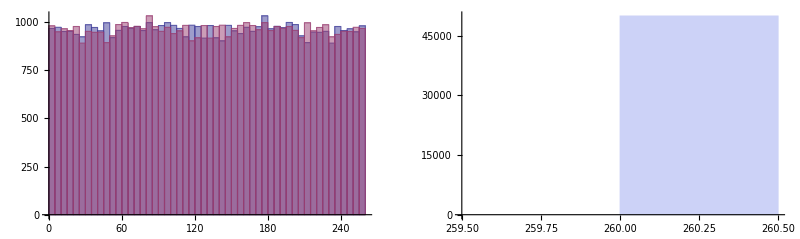

```mathematica
GraphicsGrid[{{
Histogram[{Table[DataObser[[i,7]],{i,1,n}],Table[DataObser[[i,8]],{i,1,n}]}],
Histogram[Table[DataObser[[i,12]],{i,1,n}],{0.5}]
}},ImageSize->800]
```

## Detector Acceptance

```mathematica
Rot1=RotationMatrix[60°,{0,-1,0}];
Rot2=RotationMatrix[60°,{0,1,0}];
```

```mathematica
MSXY1=Table[DataObser[[i,1]] 1022.37/1400 Normalize[ArrgDataList[[i,1]][[2;;4]]],{i,1,n}];
MSXY2=Table[DataObser[[i,2]] 1022.37/1400 Normalize[ArrgDataList[[i,2]][[2;;4]]],{i,1,n}];
MWDCcoord1=Table[Rot1.MSXY1[[i]],{i,1,n}];
MWDCcoord2=Table[Rot2.MSXY2[[i]],{i,1,n}];
(* Filter events by MWDC detection area , Filter will select MWDC pos and ToF*)
AccpDataList=Select[
Table[
If[
(f[-MWDCcoord1[[i,1]]]>Abs[MWDCcoord1[[i,2]]]) &&( f[MWDCcoord2[[i,1]]]>Abs[MWDCcoord2[[i,2]]]),
DataList[[i]],
{{0,0,0},{0,0,0}}
]
,{i,1,n}]
,#≠{{0,0,0},{0,0,0}}&];
AccpXY=Select[
Table[
If[
(f[-MWDCcoord1[[i,1]]]>Abs[MWDCcoord1[[i,2]]]) &&( f[MWDCcoord2[[i,1]]]>Abs[MWDCcoord2[[i,2]]]),
{MWDCcoord1[[i]],MWDCcoord2[[i]]},
{{0,0,0},{0,0,0}}
]
,{i,1,n}]
,#≠{{0,0,0},{0,0,0}}&];
m=Length[AccpDataList]
```

5459

```mathematica
AccpObser=Observable[AccpDataList];
```

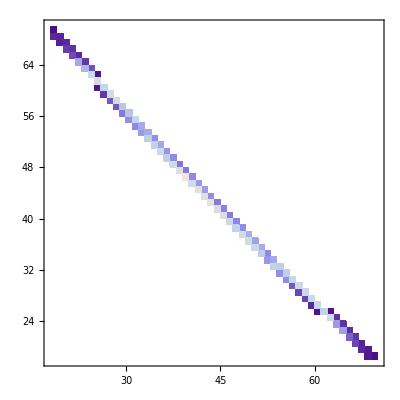

```mathematica
DensityHistogram[
Table[{AccpObser[[i,5,1]],AccpObser[[i,6,1]]}180/π,{i,1,m}],{{0, 100,1},{0,100,1}}
]
```

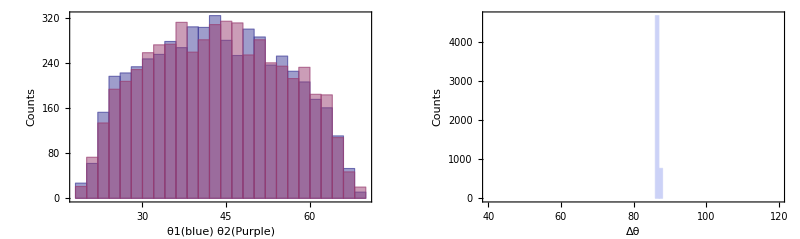

```mathematica
GraphicsGrid[{{
Histogram[{Table[AccpObser[[i,5,1]] 180/π,{i,1,m}],Table[AccpObser[[i,6,1]] 180/π,{i,1,m}]},Frame->True,FrameLabel-> {"θ1(blue) θ2(Purple)","Counts"}],
Histogram[Table[(AccpObser[[i,5,1]]+AccpObser[[i,6,1]])180/π,{i,1,m}],{40,120,1},Frame->True,FrameLabel-> {"Δθ","Counts"}]
}},ImageSize->800]
```

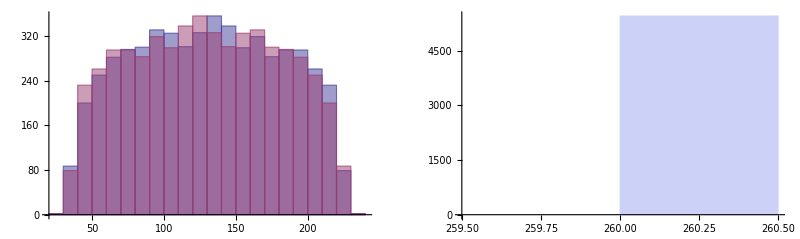

```mathematica
GraphicsGrid[{{
Histogram[{Table[AccpObser[[i,7]],{i,1,m}],Table[AccpObser[[i,8]],{i,1,m}]}],
Histogram[Table[AccpObser[[i,12]],{i,1,m}],{0.5}]
}},ImageSize->800]
```

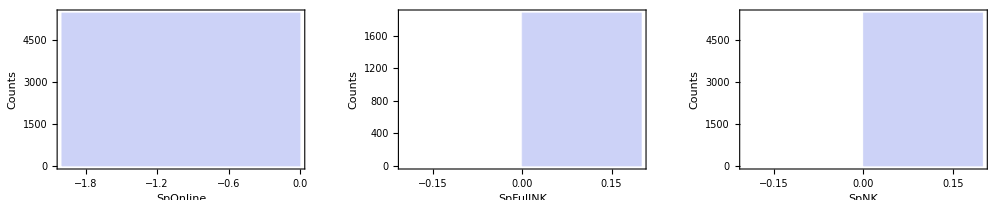

```mathematica
GraphicsGrid[{{
Histogram[Table[AccpObser[[i,11]],{i,1,m}],{2},Frame->True,FrameLabel-> {"SpOnline","Counts"}],
Histogram[Table[AccpObser[[i,13]],{i,1,m}],{0.2},Frame->True,FrameLabel-> {"SpFullNK","Counts"}],
Histogram[Table[AccpObser[[i,14]],{i,1,m}],{0.2},Frame->True,FrameLabel-> {"SpNK","Counts"}]
}},ImageSize->1000]
```

## Energy Lost

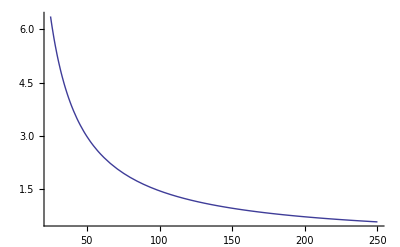

```mathematica
Plot[140/(x-3),{x,25,250},PlotRange->{0,All}]
```

```mathematica
engLost1=Table[KE[ArrgDataList[[i,1]],mp]-RandomVariate[NormalDistribution[140/(KE[ArrgDataList[[i,1]],mp]-3),0.2]],{i,1,m}];
engLost2=Table[KE[ArrgDataList[[i,2]],mp]-RandomVariate[NormalDistribution[140/(KE[ArrgDataList[[i,2]],mp]-3),0.2]],{i,1,m}];
```

```mathematica
MSDataList=Table[{
Join[{mp+engLost1[[i]]},√(2mp engLost1[[i]]+engLost1[[i]]^2)Normalize[ArrgDataList[[i,1,2;;4]]]],
Join[{mp+engLost2[[i]]},√(2mp engLost2[[i]]+engLost2[[i]]^2)Normalize[ArrgDataList[[i,2,2;;4]]]]
},{i,1,m}];
MSObser=Observable[MSDataList];
```

```mathematica
(* Skipping *)
MSDataList=AccpDataList;
MSObser=AccpObser;
```

## Detector Resolution

```mathematica
(* the change of ToF but not angle *)
σTof=0.5;
σX=1;
σY=3;
ToF1=Table[MSObser[[i,3]]+RandomVariate[NormalDistribution[0,σTof]],{i,1,m}];
ToF2=Table[MSObser[[i,4]]+RandomVariate[NormalDistribution[0,σTof]],{i,1,m}];
Pos1=Table[
Rot2.{
AccpXY[[i,1,1]]+RandomVariate[NormalDistribution[0,σX]],
AccpXY[[i,1,2]]+RandomVariate[NormalDistribution[0,σY]],
AccpXY[[i,1,3]]},{i,1,m}];
Pos2=Table[
Rot1.{
AccpXY[[i,2,1]]+RandomVariate[NormalDistribution[0,σX]],
AccpXY[[i,2,2]]+RandomVariate[NormalDistribution[0,σY]],
AccpXY[[i,2,
3]]},{i,1,m}];
Graphics3D[{
Arrow[{{0,0,0},{0,0,1400}}],
Arrow[{{0,0,0},Rot1.{0,0,1400}}],
Arrow[{{0,0,0},Rot2.{0,0,1400}}],
Point[Pos1],
Point[Pos2]
}]
FL1=Table[Norm[Pos1[[i]]] 1400/1022.37,{i,1,m}];
β1=Table[FL1[[i]]/(ToF1[[i]] c),{i,1,m}];
T1=Table[mp/(√(1-β1[[i]]^2))-mp,{i,1,m}];
FL2=Table[Norm[Pos2[[i]]] 1400/1022.37,{i,1,m}];
β2=Table[FL2[[i]]/(ToF2[[i]] c),{i,1,m}];
T2=Table[mp/(√(1-β2[[i]]^2))-mp,{i,1,m}];
```

-Graphics3D-

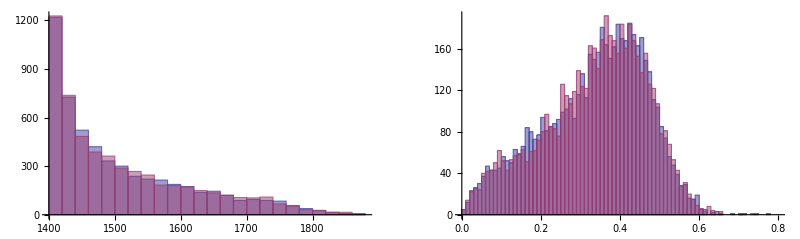

```mathematica
GraphicsGrid[{{Histogram[{FL1,FL2}],Histogram[{β1,β2},{0,0.8,0.01}]}},ImageSize->800]
```

```mathematica
Measure=Table[
{Join[{T1[[i]]+mp},√(2 mp T1[[i]]+T1[[i]]^2)Normalize[Pos1[[i]]]],
Join[{T2[[i]]+mp},√(2 mp T2[[i]]+T2[[i]]^2)Normalize[Pos2[[i]]]]
},{i,1,m}];
MeasureObser=Observable[Measure];
```

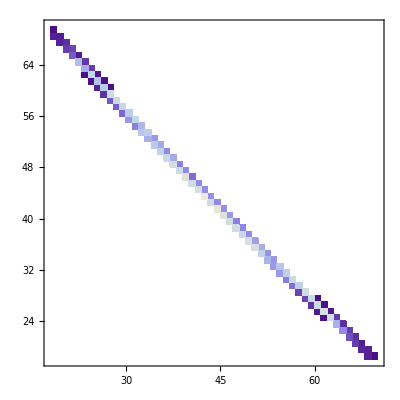

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,5,1]],MeasureObser[[i,6,1]]}180/π,{i,1,m}],{{0, 100,1},{0,100,1}}
]
```

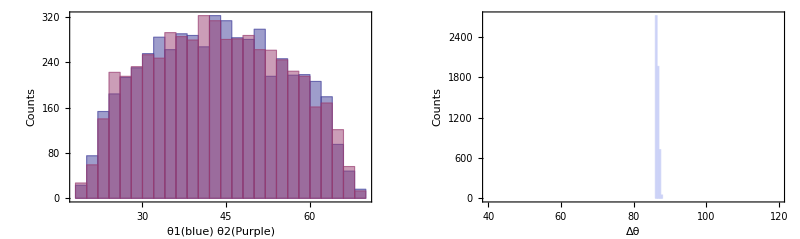

```mathematica
GraphicsGrid[{{
Histogram[{Table[MeasureObser[[i,5,1]] 180/π,{i,1,m}],Table[MeasureObser[[i,6,1]] 180/π,{i,1,m}]},Frame->True,FrameLabel-> {"θ1(blue) θ2(Purple)","Counts"}],
Histogram[Table[(MeasureObser[[i,5,1]]+MeasureObser[[i,6,1]])180/π,{i,1,m}],{40,120,0.5},Frame->True,FrameLabel-> {"Δθ","Counts"}]
}},ImageSize->800]
```

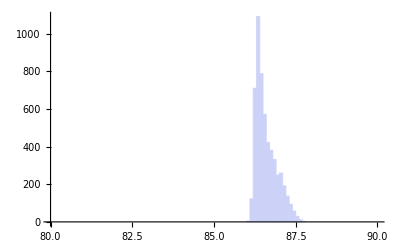

```mathematica
Histogram[Table[(MeasureObser[[i,5,1]]+MeasureObser[[i,6,1]])180/π,{i,1,m}],{80,90,0.1}]
```

Greater::nord: Invalid comparison with -3.11664 + 1.11022×10^-16\ ⅈ attempted.

Greater::nord: Invalid comparison with -2.92879 + 0.\ ⅈ attempted.

Greater::nord: Invalid comparison with -3.0521 + 1.11022×10^-16\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

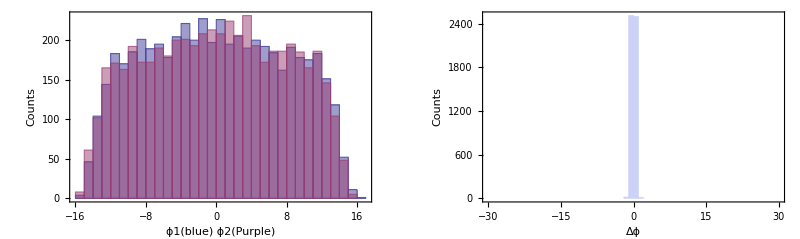

```mathematica
GraphicsGrid[{{
Histogram[{Table[MeasureObser[[i,5,2]] 180/π,{i,1,m}],Table[ϕCorr[MeasureObser[[i,6,2]]] 180/π,{i,1,m}]},Frame->True,FrameLabel-> {"ϕ1(blue) ϕ2(Purple)","Counts"}],
Histogram[Table[(MeasureObser[[i,5,2]]+ϕCorr[MeasureObser[[i,6,2]]])180/π,{i,1,m}],{-30,30,1},Frame->True,FrameLabel-> {"Δϕ","Counts"}]
}},ImageSize->800]
```

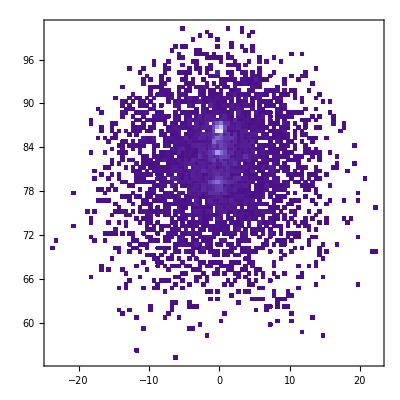

```mathematica
DensityHistogram[
Table[{(MeasureObser[[i,5,2]]+ϕCorr[MeasureObser[[i,6,2]]])180/π,(MeasureObser[[i,5,1]]+MeasureObser[[i,6,1]])180/π},{i,1,m}],{{-30,30,0.5},{40,120,0.5}}
]
```

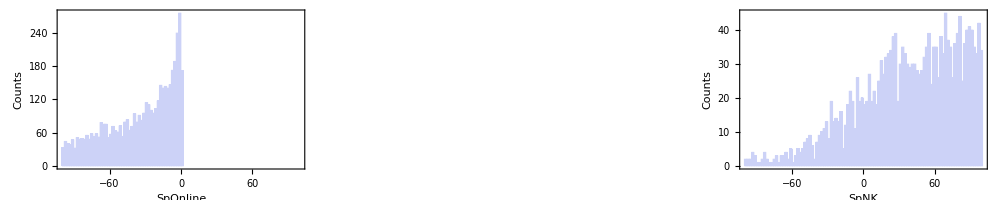

```mathematica
GraphicsGrid[{{
Histogram[Table[MeasureObser[[i,11]],{i,1,m}],{-100,100,2},Frame->True,FrameLabel-> {"SpOnline","Counts"}],
Histogram[Table[MeasureObser[[i,13]],{i,1,m}],{-100,100,2},Frame->True,FrameLabel-> {"SpFullNK","Counts"}],
Histogram[Table[MeasureObser[[i,14]],{i,1,m}],{-100,100,2},Frame->True,FrameLabel-> {"SpNK","Counts"}]
}},ImageSize->1000]
```

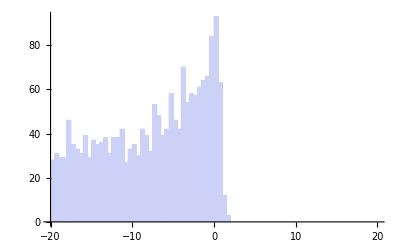

```mathematica
Histogram[Table[MeasureObser[[i,11]],{i,1,m}],{-20,20,0.5}]
```

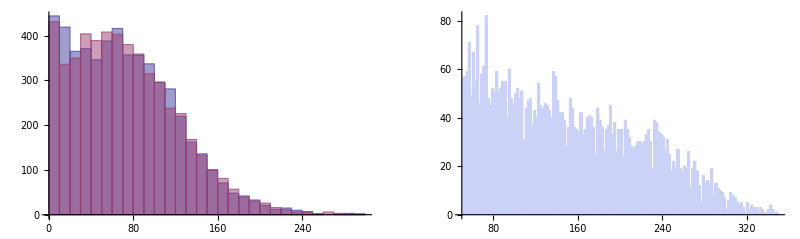

```mathematica
GraphicsGrid[{{
Histogram[{Table[MeasureObser[[i,7]],{i,1,m}],Table[MeasureObser[[i,8]],{i,1,m}]},{0,300,10}],
Histogram[Table[MeasureObser[[i,12]],{i,1,m}],{50, 350,2}]}},ImageSize->800]
```

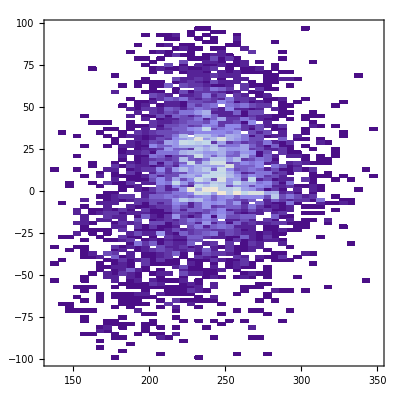

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,12]],MeasureObser[[i,11]]},{i,1,m}],{{0,350,5},{-100,100,2}}
]
```